```mathematica
SetDirectory[NotebookDirectory[]] ;
data = Import["solution.dat"];
dataquad = Import["solution_quad.dat"];
datasimple= Import["solution_simple.dat"];
datadegenerate= Import["solution_degenerate.dat"];
datasingular= Import["solution_singular.dat"];
```

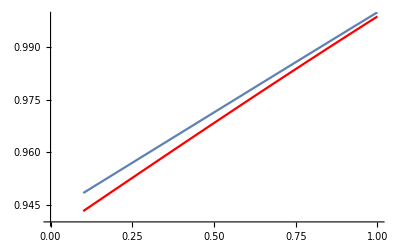

```mathematica
Show[ListLinePlot[dataquad,PlotStyle->Red],ListLinePlot[datasimple],ListLinePlot[datadegenerate]]
```

```mathematica
ListPointPlot3D[datasingular, AxesLabel->{"x", "y", "Res"},AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
ContourPlot[]
```

```mathematica
(*eq={y[x]-λ∫_a^b k[x,s]*y[s]ⅆs==f[x]};
params = {a->0,b->1,k[x,s]->0.5(1-x *Cos[x *s]),f[x]->0.5(1+Sin[x])};
params1 = {a->0,b->1,k[x,s]->1,f[x]->0.5(1+Sin[x])};*)
```

```mathematica
(*eq=eq/.params;
DSolveValue[eq[[1]],y[x],x]*)
```